# Local Optimization on the Gaussian manifold

This notebook is intended as a guide to using the optimization algorithm performing gradient descent over the manifold of pure bosonic or fermionic Gaussian states.

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"Packages (.m files)"];
<<GaussianOptimization`
```

# The GaussianOptimization.m package and its functions

All functions included in the package, in alphabetical order:

```mathematica
?"GaussianOptimization`*"
```

## Optimization algorithm

```mathematica
?GOOptimize
```

{ F_final , M_final , N_corrections , {F} , {all F} , {|∇|} }=GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]

ProblemSpecific={f,df} 
SystemSpecific={J_0,listM_0,K,G}
ProcedureSpecific={tol_F,tol_∇,lim_iterations ,step size sub-routine,track all trajectories?}

For a more detailed explanation of the input arguments, see the guide to setting up a customization at the end of this document!

## Basic Tools and Fundamental definitions

Symplectic forms and Covariance matrices

For Bosonic states

```mathematica
?GOΩqpqp
```

GOΩqpqp[N] generates Ω in basis (q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOΩqqpp
```

GOΩqqpp[N] generates Ω in basis (q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOΩaabb
```

GOΩaabb[N] generates Ω in basis (a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOΩabab
```

GOΩabab[N] generates Ω in basis (a_1,b_1,a_2,b_2,...) for N deg. of freedom

For Fermionic states

```mathematica
?GOGqpqp
```

GOGqpqp[N] generates G in basis (q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOGqqpp
```

GOGqqpp[N] generates G in basis (q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOGaabb
```

GOGaabb[N] generates G in basis (a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOGabab
```

GOGabab[N] generates G in basis (a_1,b_1,a_2,b_2,...) for N deg. of freedom

Transforming between structures

```mathematica
?GOTransformGtoJ
```

GOTransformGtoJ[G,'Gbasis','Jbasis'] generates J in Jbasis associated with G in Gbasis

```mathematica
?GOTransformΩtoJ
```

GOTransformΩtoJ[Ω,'Ωbasis','Jbasis'] generates J in Jbasis associated with Ω in Ωbasis

```mathematica
?GOTransformJtoG
```

GOTransformJtoG[J,'Jbasis','Gbasis'] generates G in Gbasis associated with J in Jbasis

```mathematica
?GOTransformJtoΩ
```

GOTransformJtoΩ[J,'Jbasis','Ωbasis'] generates Ω in Ωbasis associated with J in Jbasis

Basis Transformation matrices

We provide basis transformation matrices for transformations between four bases (note that b_i are the respective annihilation operators):
 (q_1,p_1,q_2,p_2,...) 	(q_1,q_2,...,p_1,p_2,...)	(a_1,b_1,a_2,b_2,...)	(a_1,a_2,...,b_1,b_2,...)

where we have defined:		a_i=1/(√2)(q_i+ⅈ p_i)  and   b_i=1/(√2)(q_i-ⅈ p_i)

Re-ordering

```mathematica
?GOqqppFROMqpqp
```

GOqqppFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOqpqpFROMqqpp
```

GOqpqpFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMabab
```

GOaabbFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOababFROMaabb
```

GOababFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

position / momentum → annihilation / creation operators

```mathematica
?GOababFROMqpqp
```

GOababFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMqpqp
```

GOaabbFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOababFROMqqpp
```

GOababFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMqqpp
```

GOaabbFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

annihilation / creation operators → position / momentum

```mathematica
?GOqpqpFROMabab
```

GOqpqpFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOqqppFROMabab
```

GOqqppFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOqpqpFROMaabb
```

GOqpqpFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOqqppFROMaabb
```

GOqqppFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

Lie algebra bases

All Lie algebra bases are generated in the basis  (q_1,p_1,q_2,p_2,...)  by convention

```mathematica
?GOSpBasis
```

SpBasis[N] generates Sp(2N,R) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

```mathematica
?GOSpBasisNoUN
```

spBasisNoUN[N] generates Sp(2N,R)/U(N) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

```mathematica
?GOSpBasisNoU1
```

spBasisNoU1[N] generates Sp(2N,R)/U(1)^N Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

```mathematica
?GOOBasis
```

OBasis[N] generates O(2N,R) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

We can also construct a compound Lie algebra basis for a system that is divided into two subsystems:

```mathematica
?GOCompoundBasis
```

GOCompoundBasis[{'basisA','basisB'},{dimA,dimB}] generates a compound Lie algebra basis with basis 'basisA' in subsystem A with dimA degrees of freedom and equivalently for subsystem B, in the basis qpqp

```mathematica
?GOSpBasisNoSp
```

GOSpBasisNoSp[N_A,N_B] generates the compound Lie algebra basis sp(2(N_A+N_B),R)/sp(2N_A,R) x sp(2N_B,R)

Metrics for the symplectic and orthogonal manifolds

```mathematica
?GOMetricSp
```

GOMetricSp[K,J_0] generates the natural metric for the symplectic manifold with Lie basis K, for an initial state J_0

```mathematica
?GOMetricO
```

GOMetricO[K,J_0] generates the natural metric for the orthogonal manifold with Lie basis K

Generating random Transformations

```mathematica
?GORandomTransformation
```

GORandomTransformation[n,'Basis'] generates a random transformation in the Lie group with algebra 'Basis'

Tools for computational efficiency

```mathematica
?GOapproxExp
```

approxExp[ϵ,K]=(1 + ϵ/2 K)/(1 - ϵ/2 K) approximates MatrixExponential[ϵX]

```mathematica
?GOlogfunction
```

logfunction[x] takes value 0 when x=0 and log[x] otherwise

```mathematica
?GOConditionalLog
```

GOConditionalLog[x] calculates MatrixLog[x] by applying logfunction to the eigenvalues of x

```mathematica
?GOinvMSp
```

invMSp[m,'Mform'] inverts a symplectic matrix m in the basis Mform as m^-1=-ΩmΩ

## Applications implemented in GaussianOptimization.m

Purifications and the standard form

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
?GOExtractStdFormΩ
```

{rlist,Tra}=GOExtractStdFormΩ[Ω]
Returns the parameters for constructing the standard form of Ω (list of the r_i and the transformation matrix Tra that puts Ω into standard form

```mathematica
?GOPurifyStandardGBoson
```

G_sta=GOPurifyStandardGBoson[rlist,N,'Gform']
Constructs the bosonic purified state convariance matrix in the basis Gform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardJBoson
```

J_sta=GOPurifyStandardJBoson[rlist,N,'Jform']
Constructs the bosonic purified state complex structure in the basis Jform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardΩFermion
```

Ω_sta=GOPurifyStandardΩFermion[rlist,N,'Ωform']
Constructs the fermionic purified state convariance matrix in the basis Ωform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardJFermion
```

J_sta=GOPurifyStandardJFermion[rlist,N,'Jform']
Constructs the fermionic purified state complex structure in the basis Jform with N degrees of freedom in the ancillary

Entanglement of Purification

```mathematica
?GORestrictionAA
```

GORestrictionAA[{dimA1, dimB1, dimA2, dimB2}] generates the restriction function for use in calculating EoP for a system decomposed into degrees of freedom {dimA1, dimB1, dimA2, dimB2}

```mathematica
?GOEoPBos
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the bosonic EoP for the given restriction

```mathematica
?GOEoPgradBos
```

GOEoPgradBos[Restriction] generates a function df[M,J_0,K,G^-1] which calculates the gradient of the bosonic EoP for the given restriction with respect to the Lie algebra basis K

```mathematica
?GOEoPFerm
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the fermionic EoP for the given restriction

```mathematica
?GOEoPgradFerm
```

GOEoPgradFerm[Restriction] generates a function df[M,J_0,K,G^-1] which calculates the gradient of the fermionic EoP for the given restriction with respect to the Lie algebra basis K

Complexity of Purification

```mathematica
?GOCoPBos
```

GOCoPBos[J_T] generates a function f[M,J_R0] which calculates the bosonic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradBos
```

GOCoPBos[J_T] generates a function df[M,J_R0,K,G^-1] which calculates the gradient of the bosonic CoP with respect to the given target state J_T and the Lie algebra basis K

```mathematica
?GOCoPFerm
```

GOCoPFerm[J_T] generates a function f[M,J_R0] which calculates the fermionic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradFerm
```

GOCoPgradFerm[J_T] generates a function df[M,J_R0,K,G^-1] which calculates the gradient of the fermionic CoP with respect to the given target state J_T and the Lie algebra basis K

Energy of quadratic Hamiltonians

```mathematica
?GOenergyBos
```

GOenergyBos[h] generates an energy function f[M,J_0] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradBos
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

```mathematica
?GOenergyFerm
```

GOenergyFerm[h] generates an energy function f[M,J_0] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradFerm
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

# Selected examples: EoP and CoP

## Bosonic Entanglement of Purification (EoP)

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In the example below, the mixed state is obtained for a system with total number of lattice sites 100 with 3 sites per subsystem in the initial system, mass term 0.1, lattice spacing 1, 
and no lattice sites separating the subsystems.

```mathematica
CM0=partialCM[100,.1,1,0,3,3]; CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
J0=GOPurifyStandardJBoson[rlist,6,"qpqp"];
```

#### 3. Generate a list of the starting points for the optimization (in this case 50 random transformations)

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[{3,3},"GOSpBasisNoSp"]}}]//SparseArray,{50}];
```

#### 4. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{3,3,3,3}];
function=GOEoPBos[Restriction]; gradient=GOEoPgradBos[Restriction];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasisNoSp"},{3,3,3,3}];
metric=GOMetricSp[LieBasis,J0];

SystemSpecific={J0,M0List,LieBasis,metric};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,10000,stepcorrection,False};
(* Here we specify that all 50 initial trajectories should be pursured until convergence *)
```

#### 7. Run the Optimization

```mathematica
{Time2,Result2}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Iteration limit reached

#### 8. Evaluate the result

Time taken: 9.20141

Final value: {0.379656}

Number of iterations: {160}

Number of total corrections: 0

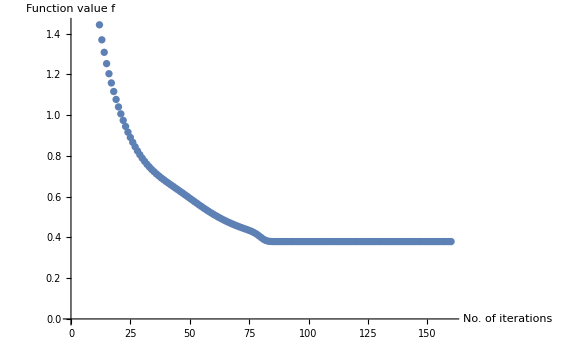

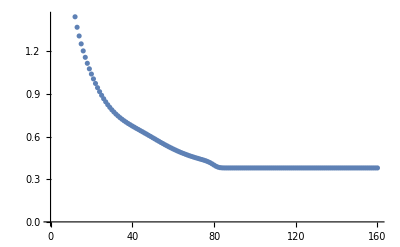

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[#, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]&/@Result[[4]]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
ListPlot/@Result[[5]]
```

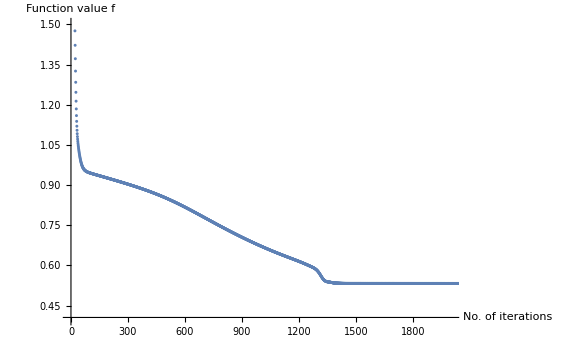

```mathematica
ListPlot[#, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->{{0,2000},{0.4,1.5}}]&/@Result[[4]]
```

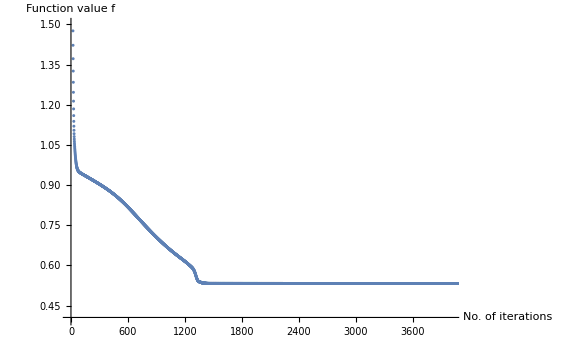

```mathematica
ListPlot[#, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->{{0,4000},{0.4,1.5}}]&/@Result[[4]]
```

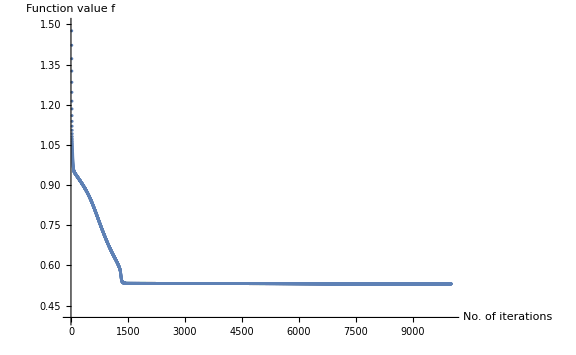

```mathematica
ListPlot[#, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->{{0,10000},{0.4,1.5}}]&/@Result[[4]]
```

## Bosonic Complexity of Purification (CoP)

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In the example below, the mixed state is obtained for a system with total number of lattice sites 100 with 3 sites per subsystem in the initial system, mass term 0.1, lattice spacing 1, 
and no lattice sites separating the subsystems.

```mathematica
CM0=partialCM[100,.1,1,0,3,3]; CM0//MatrixForm
```

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,6,"qpqp"];
JR0=GOTransformGtoJ[IdentityMatrix[24],"qpqp","qpqp"];
```

#### 3. Generate a list of the starting points for the optimization (in this case 10 random transformations)

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[12,"GOSpBasis"]}}]//SparseArray,{10}];
```

#### 4. Define the problem-specific input arguments

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOCompoundBasis[{"None","GOSpBasis"},{6,6}];
metric=GOMetricSp[LieBasis,JR0];

SystemSpecific={JR0,M0List,LieBasis,metric};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-6,10^-10,∞,stepcorrection,False};
```

#### 7. Execute the optimization

```mathematica
{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

#### 8. Evaluate the result

```mathematica
Print["Time taken: ",Time];
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4,1]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
(* This looks like just one trajectory but it is in fact four identical trajectories! *)
```

## Fermionic Entanglement of Purification (EoP)

```mathematica
NN=30; (* Total number lattice sites *)
J=1;h=.5;γ=.5; (* XY model parameter*)
dimA1=4; dimB1=4; (* dofs of chosen subystems *)
d=0; (* distance subsystems *)
dimA2=dimA1;dimB2= dimB1;(* purifying dofs, dimA2+dimB2 ≥ dimA1+dimB1 *)
```

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for the XY model

```mathematica
ϵ[k_]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]=-J Cos[k]-h;
b[k_]=γ J Sin[k];
u[k_]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In this case we are generating a covariance matrix for a system with a total of 10 lattice sites and partitioning it into two adjacent subsystems containing 2 lattice sites each.

```mathematica
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0;
Ωblock=1/NN Table[Sum[(Abs[v[2π k/NN]]^2-Abs[u[2π k/NN]]^2//N)Cos[2π k(j-l)/NN]+2Im[v[2π k/NN]u[2π k/NN]]Sin[2π k(j-l)/NN],{k,0,NN-1}],{j,1,NN},{l,1,NN}];
ΩΩ=ArrayFlatten[({{0, Ωblock}, {-Transpose[Ωblock], 0}})];JJ=ΩΩ;
```

```mathematica
dim1=dimA1;dim2=dimB1;dim=NN;
indices1=Thread[{Table[x,{x,dim1}],Table[x+dim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+dim,{x,dim2}]}]//Flatten[#,1]&;
indices=Join[indices1,indices2];

Tran=GOqpqpFROMqqpp[dim]; ΩΩqpqp=Tran.ΩΩ.Transpose[Tran];
Ω0=ΩΩqpqp[[indices,indices]]; Ω0//MatrixForm
```

(0. | 0. | 0.296657 | 0.0000895099 | 0. | 0. | 0.123704 | -0.000139593 | 0. | 0. | -0.0392786 | 5.8775×10^-6 | 0. | 0. | 0.00553502 | 0.000439765
0. | 0. | 0.0000895099 | 0.296657 | 0. | 0. | -0.000139593 | 0.123704 | 0. | 0. | 5.8775×10^-6 | -0.0392786 | 0. | 0. | 0.000439765 | 0.00553502
-0.296657 | -0.0000895099 | 0. | 0. | -0.88587 | 0.0000154959 | 0. | 0. | 0.323432 | 0.0000210988 | 0. | 0. | -0.0196949 | -0.0000301449 | 0. | 0.
-0.0000895099 | -0.296657 | 0. | 0. | 0.0000154959 | -0.88587 | 0. | 0. | 0.0000210988 | 0.323432 | 0. | 0. | -0.0000301449 | -0.0196949 | 0. | 0.
0. | 0. | 0.88587 | -0.0000154959 | 0. | 0. | 0.296657 | 0.0000895099 | 0. | 0. | 0.123704 | -0.000139593 | 0. | 0. | -0.0392786 | 5.8775×10^-6
0. | 0. | -0.0000154959 | 0.88587 | 0. | 0. | 0.0000895099 | 0.296657 | 0. | 0. | -0.000139593 | 0.123704 | 0. | 0. | 5.8775×10^-6 | -0.0392786
-0.123704 | 0.000139593 | 0. | 0. | -0.296657 | -0.0000895099 | 0. | 0. | -0.88587 | 0.0000154959 | 0. | 0. | 0.323432 | 0.0000210988 | 0. | 0.
0.000139593 | -0.123704 | 0. | 0. | -0.0000895099 | -0.296657 | 0. | 0. | 0.0000154959 | -0.88587 | 0. | 0. | 0.0000210988 | 0.323432 | 0. | 0.
0. | 0. | -0.323432 | -0.0000210988 | 0. | 0. | 0.88587 | -0.0000154959 | 0. | 0. | 0.296657 | 0.0000895099 | 0. | 0. | 0.123704 | -0.000139593
0. | 0. | -0.0000210988 | -0.323432 | 0. | 0. | -0.0000154959 | 0.88587 | 0. | 0. | 0.0000895099 | 0.296657 | 0. | 0. | -0.000139593 | 0.123704
0.0392786 | -5.8775×10^-6 | 0. | 0. | -0.123704 | 0.000139593 | 0. | 0. | -0.296657 | -0.0000895099 | 0. | 0. | -0.88587 | 0.0000154959 | 0. | 0.
-5.8775×10^-6 | 0.0392786 | 0. | 0. | 0.000139593 | -0.123704 | 0. | 0. | -0.0000895099 | -0.296657 | 0. | 0. | 0.0000154959 | -0.88587 | 0. | 0.
0. | 0. | 0.0196949 | 0.0000301449 | 0. | 0. | -0.323432 | -0.0000210988 | 0. | 0. | 0.88587 | -0.0000154959 | 0. | 0. | 0.296657 | 0.0000895099
0. | 0. | 0.0000301449 | 0.0196949 | 0. | 0. | -0.0000210988 | -0.323432 | 0. | 0. | -0.0000154959 | 0.88587 | 0. | 0. | 0.0000895099 | 0.296657
-0.00553502 | -0.000439765 | 0. | 0. | 0.0392786 | -5.8775×10^-6 | 0. | 0. | -0.123704 | 0.000139593 | 0. | 0. | -0.296657 | -0.0000895099 | 0. | 0.
-0.000439765 | -0.00553502 | 0. | 0. | -5.8775×10^-6 | 0.0392786 | 0. | 0. | 0.000139593 | -0.123704 | 0. | 0. | -0.0000895099 | -0.296657 | 0. | 0.)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormΩ[Ω0];
J0=GOPurifyStandardJFermion[rlist,dimA2+dimB2,"qpqp"];
rlist
```

{0.00302353,0.00315138,0.055216,0.055614,0.0784274,0.0786285,0.7647,0.76509}

#### 3. Generate a list of the starting points for the optimization (in this case 50 random transformations)

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[{dimA2,dimB2},"GOOBasis"]}}]//SparseArray,{50}];
```

#### 4. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPFerm[Restriction]; gradient=GOEoPgradFerm[Restriction];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOCompoundBasis[{"None","GOOBasis"},{dimA1,dimB1,dimA2,dimB2}];
metric=GOMetricO[LieBasis];

SystemSpecific={J0,M0List,LieBasis,metric};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-9,10^-10,∞,stepcorrection,False};
```

#### 7. Run the Optimization

```mathematica
{time,Result}=AbsoluteTiming[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

#### 8. Evaluate the result

Final value: {0.752427}

Number of iterations: {2852}

Number of total corrections: 5687

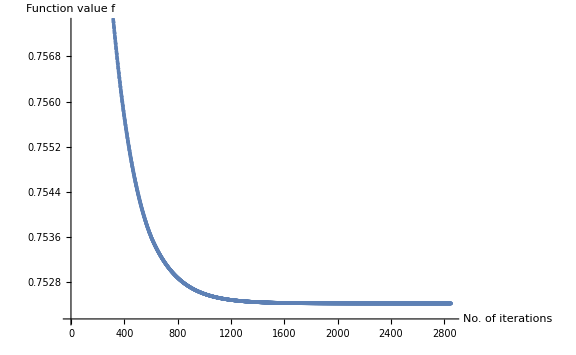

```mathematica
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[#, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]&/@Result[[4]]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
time
```

86.1372

## Fermionic Complexity of Purification (CoP)

```mathematica
NN=30; (* Total number lattice sites *)
J=1;h=.5;γ=.5; (* XY model parameter*)
dimA1=4; dimB1=4; (* dofs of chosen subystems *)
d=0; (* distance subsystems *)
dimA2=dimA1;dimB2= dimB1;(* purifying dofs, dimA2+dimB2 ≥ dimA1+dimB1 *)
JR=GOTransformΩtoJ[GOΩqpqp[dimA1+dimB1+dimA2+dimB2],"qpqp","qpqp"]; (* reference state*)
```

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for the XY model

```mathematica
ϵ[k_]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]=-J Cos[k]-h;
b[k_]=γ J Sin[k];
u[k_]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In this case we are generating a covariance matrix for a system with a total of 10 lattice sites and partitioning it into two adjacent subsystems containing 2 lattice sites each.

```mathematica
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0;
Ωblock=1/NN Table[Sum[(Abs[v[2π k/NN]]^2-Abs[u[2π k/NN]]^2//N)Cos[2π k(j-l)/NN]+2Im[v[2π k/NN]u[2π k/NN]]Sin[2π k(j-l)/NN],{k,0,NN-1}],{j,1,NN},{l,1,NN}];
ΩΩ=ArrayFlatten[({{0, Ωblock}, {-Transpose[Ωblock], 0}})];JJ=ΩΩ;
```

```mathematica
dim1=dimA1;dim2=dimB1;dim=NN;
indices1=Thread[{Table[x,{x,dim1}],Table[x+dim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+dim,{x,dim2}]}]//Flatten[#,1]&;
indices=Join[indices1,indices2];

Tran=GOqpqpFROMqqpp[dim]; ΩΩqpqp=Tran.ΩΩ.Transpose[Tran];
Ω0=ΩΩqpqp[[indices,indices]]; Ω0//MatrixForm
```

(0. | 0. | 0.296657 | 0.0000895099 | 0. | 0. | 0.123704 | -0.000139593 | 0. | 0. | -0.0392786 | 5.8775×10^-6 | 0. | 0. | 0.00553502 | 0.000439765
0. | 0. | 0.0000895099 | 0.296657 | 0. | 0. | -0.000139593 | 0.123704 | 0. | 0. | 5.8775×10^-6 | -0.0392786 | 0. | 0. | 0.000439765 | 0.00553502
-0.296657 | -0.0000895099 | 0. | 0. | -0.88587 | 0.0000154959 | 0. | 0. | 0.323432 | 0.0000210988 | 0. | 0. | -0.0196949 | -0.0000301449 | 0. | 0.
-0.0000895099 | -0.296657 | 0. | 0. | 0.0000154959 | -0.88587 | 0. | 0. | 0.0000210988 | 0.323432 | 0. | 0. | -0.0000301449 | -0.0196949 | 0. | 0.
0. | 0. | 0.88587 | -0.0000154959 | 0. | 0. | 0.296657 | 0.0000895099 | 0. | 0. | 0.123704 | -0.000139593 | 0. | 0. | -0.0392786 | 5.8775×10^-6
0. | 0. | -0.0000154959 | 0.88587 | 0. | 0. | 0.0000895099 | 0.296657 | 0. | 0. | -0.000139593 | 0.123704 | 0. | 0. | 5.8775×10^-6 | -0.0392786
-0.123704 | 0.000139593 | 0. | 0. | -0.296657 | -0.0000895099 | 0. | 0. | -0.88587 | 0.0000154959 | 0. | 0. | 0.323432 | 0.0000210988 | 0. | 0.
0.000139593 | -0.123704 | 0. | 0. | -0.0000895099 | -0.296657 | 0. | 0. | 0.0000154959 | -0.88587 | 0. | 0. | 0.0000210988 | 0.323432 | 0. | 0.
0. | 0. | -0.323432 | -0.0000210988 | 0. | 0. | 0.88587 | -0.0000154959 | 0. | 0. | 0.296657 | 0.0000895099 | 0. | 0. | 0.123704 | -0.000139593
0. | 0. | -0.0000210988 | -0.323432 | 0. | 0. | -0.0000154959 | 0.88587 | 0. | 0. | 0.0000895099 | 0.296657 | 0. | 0. | -0.000139593 | 0.123704
0.0392786 | -5.8775×10^-6 | 0. | 0. | -0.123704 | 0.000139593 | 0. | 0. | -0.296657 | -0.0000895099 | 0. | 0. | -0.88587 | 0.0000154959 | 0. | 0.
-5.8775×10^-6 | 0.0392786 | 0. | 0. | 0.000139593 | -0.123704 | 0. | 0. | -0.0000895099 | -0.296657 | 0. | 0. | 0.0000154959 | -0.88587 | 0. | 0.
0. | 0. | 0.0196949 | 0.0000301449 | 0. | 0. | -0.323432 | -0.0000210988 | 0. | 0. | 0.88587 | -0.0000154959 | 0. | 0. | 0.296657 | 0.0000895099
0. | 0. | 0.0000301449 | 0.0196949 | 0. | 0. | -0.0000210988 | -0.323432 | 0. | 0. | -0.0000154959 | 0.88587 | 0. | 0. | 0.0000895099 | 0.296657
-0.00553502 | -0.000439765 | 0. | 0. | 0.0392786 | -5.8775×10^-6 | 0. | 0. | -0.123704 | 0.000139593 | 0. | 0. | -0.296657 | -0.0000895099 | 0. | 0.
-0.000439765 | -0.00553502 | 0. | 0. | -5.8775×10^-6 | 0.0392786 | 0. | 0. | 0.000139593 | -0.123704 | 0. | 0. | -0.0000895099 | -0.296657 | 0. | 0.)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormΩ[Ω0];
JT=GOPurifyStandardJFermion[rlist,dimA2+dimB2,"qpqp"];
rlist
```

{0.00302353,0.00315138,0.055216,0.055614,0.0784274,0.0786285,0.7647,0.76509}

#### 3. Generate a list of the starting points for the optimization (in this case 50 random transformations)

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GORandomTransformation[{dimA2,dimB2},"GOOBasis"]}}]//SparseArray,{50}];
```

#### 4. Define the problem-specific input arguments

```mathematica
function=GOCoPFerm[JT]; gradient=GOCoPgradFerm[JT];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOCompoundBasis[{"None","GOOBasis"},{dimA1,dimB1,dimA2,dimB2}];
metric=GOMetricO[LieBasis];

SystemSpecific={JR,M0List,LieBasis,metric};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2;
ProcedureSpecific={10^-9,10^-10,∞,stepcorrection,False};
```

#### 7. Run the Optimization

```mathematica
{time,Result}=AbsoluteTiming[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

$Aborted

#### 8. Evaluate the result

Final value: {1.65691}

Number of iterations: {804}

Number of total corrections: 2374

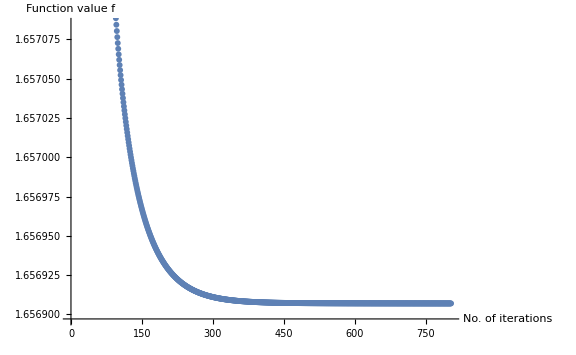

```mathematica
Print["Final value: ",Result[[1,All]]];
Print["Number of iterations: ",Length/@Result[[4]]];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[#, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]&/@Result[[4]]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

# Setting up a custom optimization

This section is intended as a concise guide to applying the GaussianOptimization.m package and its functions to an arbitrary optimization problem.
As shown in the function description for GOOptimize above, the input arguments for the optimization can be grouped into three categories:

#### 1. Problem-Specific input arguments

These are the arguments that are related specifically to the physical quantity under investigation. They are:

f -- The function to be optimized (must be a function of the transformation M, and the initial state complex structure J_0)

df -- The gradient associated with the function to be optimized (must be a function of the transformation M, the initial state complex structure J_0, the Lie algebra basis K, and the inverse metric G^-1)

#### 2. System-Specific input arguments

These are the arguments that are related to the geometry of the manifold over which the optimization is conducted, including also the points in the manifold, from which the optimization is initialized. Changing the system-specific arguments while keeping all other arguments the same means changing only the landscape on which the gradient descent is performed.
Import note: All system specific input arguments must be in the basis (q_1,p_1,q_2,p_2,...)!

J_0 -- The initial state complex structure

{M_0} -- A list of the initial transformations to be applied to J_0 (together with J_0, these transformations parametrize the starting points for the gradient descent)

{K_i} -- The Lie algebra basis

G^-1 -- The inverse natural metric

These input arguments are key to the theory underlying this optimization algorithm: The inverse natural metric is used by the gradient function to calculate a consistent value for the gradient vector, independent of basis choice. More importantly, it should be noted that any constraints on the optimization are implemented by restricting the Lie algebra basis to those elements K_i which generate transformations that only transform within the restricted class of states of interest.

#### 3. Procedure-Specific input arguments

These input arguments specify parameters relating to the numerical implementation of the optimization. Firstly, this includes three stopping criteria:

tol_F -- Tolerance on the function values (stopping criterion: (F_(n+1)-F_n)/F_(n+1)<tol_F)

tol_F -- Tolerance on the function values (stopping criterion: (F_(n+1)-F_n)/F_(n+1)<tol_F)

lim_iter  -- Limit on the number of iterations (stopping criterion: n>lim_iter; the default value of this argument is ∞)

The algorithm is terminated as soon as any of the three stopping criteria is violated by all of the trajectories still under consideration.

Secondly, the procedure-specific input arguments include the sub-routine for correcting the step size in the case where F_(n+1)>F_ninitially. This subroutine must be of function of the current step size only, which returns only the new step size. The most rudimentary implementation, used in the examples above, is simply step(ϵ)=ϵ/2.

Thirdly, the input arguments include optional arguments for debugging modes of the algorithm. In particular, at the moment there is only one such optional parameter, which tales either True or False as values, where False corresponds to running the algorithm in its most efficient version, without debugging.

track all trajectories? -- This completes the full optimization procedure for all starting points, rather than only the most promising trajectories